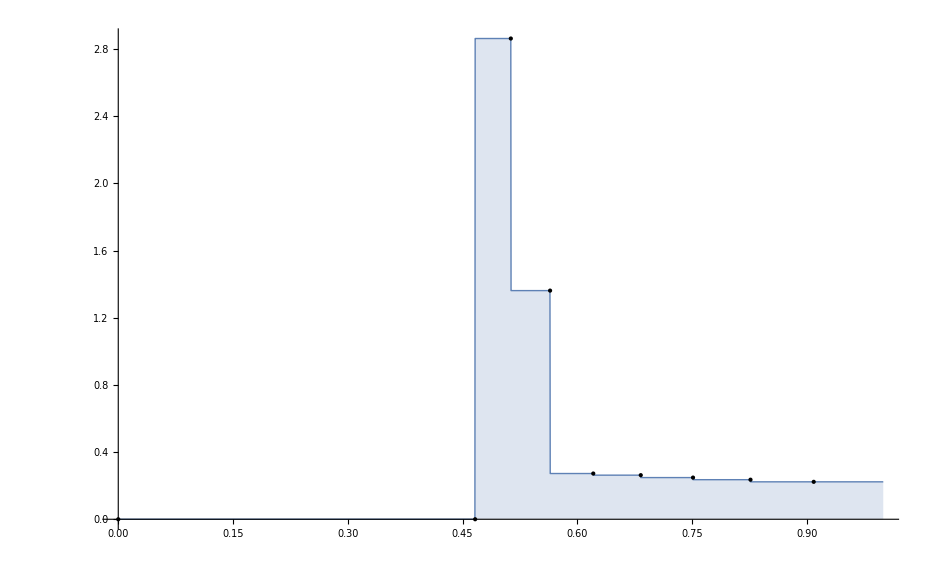

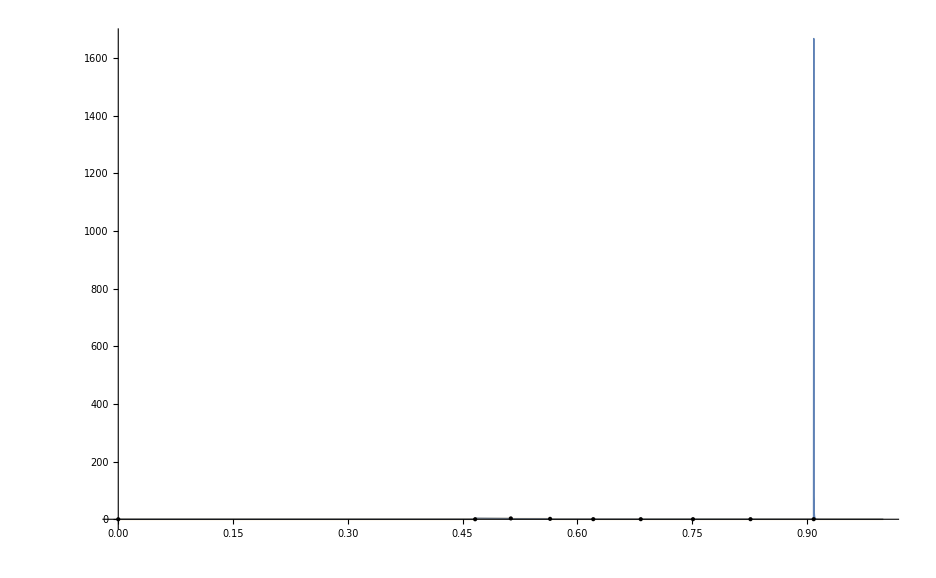

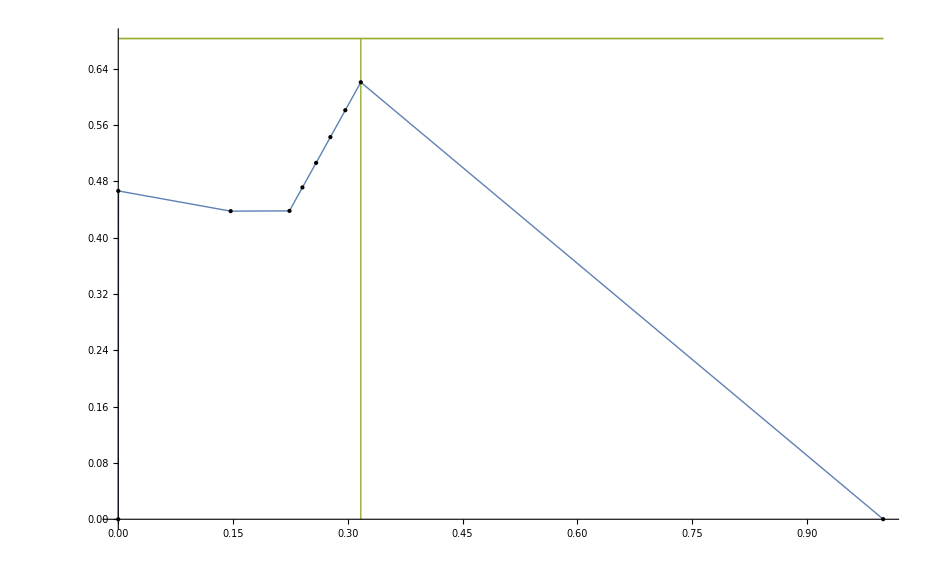

Optimal Revenue = 0.620856

------------------

Real Discrete Revenue = 0.540459

Real Discrete Ratio = 0.870506

------------------

Charged Revenue = 0.54069

Charged Ratio = 0.870879

```mathematica
id=56; (*620, 629 important!*)

(*import data from log*)
opt=getOpt[id];
iopt=getIopt[id];
ww=getW[id];
xx=getX[id];
yy=getY[id];
zz=getZ[id];
dd1=getD1[id];
dd2=getD2[id];
dd3=getD3[id];
pp=getP[id];
rr=getR[id];
oo=getO[id];
bb=getB[id];

(*define functions*)
n = Length[zz];
w[i_]:=If[ww[[i]]≤10^(-11),0,ww[[i]]];
x[i_,j_,k_]:=If[xx[[i]][[j]][[k]]≤10^(-11),0,xx[[i]][[j]][[k]]];
y[i_,j_]:=If[yy[[i]][[j]]≤10^(-11),0,yy[[i]][[j]]];
z[i_]:=If[zz[[i]]≤10^(-11),0,zz[[i]]];

s[i_]:=Sum[z[j],{j,1,i}];
sy[i_,j_]:=Sum[Sum[y[k,l],{l,1,j}],{k,1,i}];
sy1[i_,j_]:=Sum[y[k,j],{k,1,i}];
syx[i_,j_,k_]:=Sum[Sum[x[l,t,k],{t,1,j}],{l,1,i}];

r[i_]:=w[i]*(1-s[i]);
c1[i_]:=(r[i+1]-r[i])/(s[i+1]-s[i]);
c2[i_]:=r[i]-c1[i]s[i];

f[p_]:=Piecewise[Join[Table[{If[(c1[i]+c2[i])/(c1[i]+p)^2≥0,(c1[i]+c2[i])/(c1[i]+p)^2,0],w[i]≤p<w[i+1]},{i,1,n-1}],{{If[(c1[n-1]+c2[n-1])/(c1[n-1]+p)^2≥0,(c1[n-1]+c2[n-1])/(c1[n-1]+p)^2,0],p==w[n]}}]];

distribution=Table[{w[i],z[i]/(w[i+1]-w[i])},{i,1,n-1}];
revenueCurve=Table[{s[i],r[i]},{i,1,n}];

(*Plots*)
Plot[{Evaluate@Interpolation[distribution,InterpolationOrder->0][x]},{x,0,1},PlotRange->All,AxesOrigin->{0,0},Epilog->{PointSize[Large],Point@distribution},Filling->Bottom,PlotStyle->Thick]

Plot[{f[x],Evaluate@Interpolation[distribution,InterpolationOrder->0][x]},{x,0,1},PlotRange->All,AxesOrigin->{0,0},Epilog->{PointSize[Small],Point@distribution},Filling->Bottom,PlotStyle->{Thick,Opacity[0.2]}]

ioptline=Line[{{s[iopt+1],0},{s[iopt+1],opt}}];
optline=Line[{{0,opt},{1,opt}}];

Plot[{Max[Evaluate@Interpolation[revenueCurve,InterpolationOrder->1][x],0],opt},{x,0,1},PlotRange->All,AxesOrigin->{0,0},Epilog->{{Directive[RGBColor[0.560181, 0.691569, 0.194885],Thick],ioptline},{Directive[RGBColor[0.560181, 0.691569, 0.194885],Thick],optline},{PointSize[Large],Point@revenueCurve}},PlotStyle->Thick]

Print["\n\n\n"]
Print["Optimal Revenue = ",r[iopt + 1]]
Print[" ------------------ "]

(*Compute Dicrete Revenue*)
revenue=0;
For[i=2,i≤n,i++,
For[j=2,j≤n,j++,
For[k=2,k≤n,k++,
pmax=Max[w[i-1],w[j-1]];
pmin=Min[w[i-1],w[j-1]];
If[pmax>=2*pmin,
If[w[k]>Max[pmax, w[2]],
revenue=revenue+Max[pmax,w[2]]*z[i]*z[j]*z[k];
]
];
If[pmax<2*pmin,
If[w[k]>Max[pmin, w[2]],
revenue=revenue+Max[pmin,w[2]]*z[i]*z[j]*z[k];
]
]
]
]
]
Print["Real Discrete Revenue = ",revenue]
Print["Real Discrete Ratio = ",revenue/r[iopt + 1]]
Print[" ------------------ "]

(*Compute Charged Revenue*)
revenue=0;
For[i=2,i≤n,i++,
For[j=2,j≤n,j++,
For[k=2,k≤n,k++,
pmax=Max[w[i-1],w[j-1]];
pmin=Min[w[i-1],w[j-1]];
If[pmax>=2*pmin,
If[w[k]>Max[pmax,0],
revenue=revenue+Max[pmax,0]*x[i,j,k];
]
];
If[pmax<2*pmin,
If[w[k]>Max[pmin,0],
revenue=revenue+Max[pmin,0]*x[i,j,k];
]
]
]
]
]
Print["Charged Revenue = ",revenue]
Print["Charged Ratio = ",revenue/r[iopt + 1]]
Print["\n\n\n"]
```

```mathematica
(*Compute Continuous Revenue*)

revMax[x1_,x2_,y_]:=If[(Max[x1,x2]≥2*Min[x1,x2])&&(y≥Max[x1,x2]),Max[x1,x2],0]
revMin[x1_,x2_,y_]:=If[(Max[x1,x2]<2*Min[x1,x2])&&(y≥Min[x1,x2]),Min[x1,x2],0]
revenue = NIntegrate[(revMax[x1,x2,y]+revMin[x1,x2,y])*f[x1]*f[x2]*f[y],{x1,0,1},{x2,0,1},{y,0,1},Method->{"GlobalAdaptive","MaxErrorIncreases"->100000},WorkingPrecision->10,MaxRecursion->100,MinRecursion->100,PrecisionGoal->10];
Print["Real Revenue = ",revenue]
Print["Real Ratio = ",revenue/r[iopt + 1]]
Print[" ------------------ "]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 100000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0616613306717481508141827462758673883428260371759230633742593 and 0.00025496704250795086256840341403826868716586116396493975115805 for the integral and error estimates.

Real Revenue = 0.06166133067

Real Ratio = 0.61661

------------------

```mathematica
Table[Table[Table[x[k,i,j],{j,1,n}],{i, 1, n}],{k,1,n}]//MatrixForm
```

(1)
 |  |  |  |

```mathematica
Table[Table[y[i,j],{j,1,n}],{i, 1, n}]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Table[z[i],{i,1,n}]//MatrixForm
```

(0
0
0
0
0
0
0
0
0.0930234
0.0104251
0.010188
0.00995925
0.00973779
0.213874
0.169113
0.117287
0.0948226
0.0845041
0.0793794
0.107686)

```mathematica
zz[1]
```

{-8.35556×10^-10,-1.30619×10^-9,-1.15532×10^-9,-4.85458×10^-10,-2.83189×10^-10,-7.75862×10^-10,-1.02458×10^-9,-6.7664×10^-10,0.0930234,0.0104251,0.010188,0.00995925,0.00973779,0.213874,0.169113,0.117287,0.0948226,0.0845041,0.0793794,0.107686}[1]

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
n
```

10

```mathematica
x[1,1,10]
```

0

```mathematica
[w[j]*(cp.sum(z[:(k+1)])-cp.sum(y[:(j+1), :(k+1)]))-w[i]*(cp.sum(z[:(k+1)])-cp.sum(y[:(i+1), :(k+1)]))+w[i]*(cp.sum(z[:(j+1)])-cp.sum(y[:(j+1), :(i+1)]))-w[j]*(cp.sum(z[:(i+1)])-cp.sum(y[:(i+1), :(j+1)]))≥w[k]*(cp.sum(z[:(j+1)])-cp.sum(y[:(k+1), :(j+1)]))-w[k]*(cp.sum(z[:(i+1)])-cp.sum(y[:(k+1), :(i+1)]))]
```

```mathematica
w[2]*(s[iopt+1]-s[2]*s[iopt+1])≥w[iopt+1]*(s[2]-s[iopt+1]*s[2])
```

False

```mathematica
w[2]*(s[iopt+1]-sy[2,iopt+1])≥w[iopt+1]*(s[2]-sy[iopt+1,2])
```

True

```mathematica
q=Table[{w[2]*(sy1[iopt+1,k]-syx[2,iopt+1,k]),w[iopt+1]*(sy1[2,k]-syx[iopt+1,2,k])},{k,1,n}]//MatrixForm
```

(6.43679×10^-8 | 0.
0.00179419 | 0.00835708
0.0000453155 | 0.000128754
0.0000126567 | 1.36523×10^-6
3.4397×10^-7 | 5.04904×10^-7
7.76625×10^-7 | 7.76625×10^-6
6.52844×10^-7 | 4.44468×10^-6
3.73607×10^-7 | 1.05324×10^-6
2.88007×10^-7 | 1.81068×10^-6
3.7261×10^-7 | 1.17701×10^-6
8.55983×10^-7 | 5.68507×10^-6
5.88376×10^-6 | 0.000024431
4.41045×10^-6 | 0.0000175909
5.17901×10^-6 | 0.000022964
3.84439×10^-6 | 0.0000127986
2.85731×10^-6 | 6.53036×10^-6
4.04061×10^-6 | 0.000013766
2.53046×10^-6 | 6.61357×10^-6)

```mathematica
w[iopt+1]*(1-s[iopt+1])*z[2]
```

0.0392902

```mathematica
z[2]
```

0.785963

```mathematica
Table[{w[iopt+1]*(1-s[iopt+1])*z[l],opt*z[l]},{l,1,n}]//MatrixForm
```

(1.15066×10^-7 | 1.29615×10^-7
0.00858911 | 0.0096751
0.0001413 | 0.000159166
9.0564×10^-6 | 0.0000102015
4.5278×10^-7 | 5.10029×10^-7
3.20164×10^-7 | 3.60645×10^-7
3.18472×10^-7 | 3.58739×10^-7
6.26066×10^-7 | 7.05224×10^-7
3.12246×10^-7 | 3.51725×10^-7
3.28987×10^-7 | 3.70584×10^-7
1.62454×10^-6 | 1.82994×10^-6
0.0000297072 | 0.0000334633
0.0000214538 | 0.0000241664
0.0000251436 | 0.0000283227
0.0000174989 | 0.0000197115
0.0000139135 | 0.0000156727
0.0000159619 | 0.0000179801
0.000013153 | 0.0000148161)

```mathematica
Table[{w[iopt+1]*(z[l]-sy1[iopt+1,l]),opt*z[l]},{l,1,n}]//MatrixForm
```

(0. | 0.
0.0334514 | 0.0334582
0.00663043 | 0.00663152
0.00283567 | 0.00283601
0.00157521 | 0.00157411
0.00100142 | 0.00100105
0.00189977 | 0.00189987
0.00115672 | 0.00115719
0.000792759 | 0.0007927
0.000649156 | 0.000649347)

```mathematica
Maximize[{(0.76-xxx)*(xxx^(1/12)),0≤xxx≤1},xxx]
```

{0.553721,{xxx→0.0584615}}

```mathematica
Manipulate[Plot[xxx*(1-xxx^yyy),{xxx,0,1}],{yyy,1,200}]
```

```mathematica
approxApprox[xxx_,yyy_]:=xxx*(1-xxx^yyy)
```

```mathematica
Simplify[D[xxx*(1-xxx^yyy),{xxx,1}]]
```

1-xxx^yyy (1+yyy)

```mathematica
argSolToR2[yyy_]:=(1/(1+yyy))^(1/yyy)
```

```mathematica
solToR[a_,yyy_]:=N[{1/argSolToR2[yyy],argSolToR2[yyy],approxApprox[argSolToR2[yyy],yyy],a*approxApprox[argSolToR2[yyy],yyy]}];
```

```mathematica
solToR[0.6,64]
```

{1.0674,0.936857,0.922444,0.553466}

```mathematica
Simplify[D[(a-xxx)*(xxx^yyy),{xxx,1}]]
```

xxx^(-1+yyy) (a yyy-xxx (1+yyy))

```mathematica
argSolToR[a_,yyy_]:=(a*yyy)/(1+yyy)
```

```mathematica
solToR[a_,yyy_]:={argSolToR[a,yyy],argSolToR[a,yyy]^(-yyy),(a-argSolToR[a,yyy])*((argSolToR[a,yyy])^yyy)}
```

```mathematica
solToR[0.63,1/50]
```

{0.0123529,1.09185,0.565686}

```mathematica
n
```

16

```mathematica
True&&False
```

False

```mathematica
revMax[0.2,0.1,0.3]*f[0.2]*f[0.1]*f[0.1]
```

0.89372

```mathematica
NIntegrate[If[x≥y,1,0]*f[x]*f[y],{x,0,1},{y,0,1},Method->{"GlobalAdaptive","MaxErrorIncreases"->100000},WorkingPrecision->10,MaxRecursion->100,MinRecursion->100,PrecisionGoal->10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 100000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.499991166534723645433478157548533305264088092881673987236172 and 1.16719908260317328889944309448959618569017568596396603877897×10^-6 for the integral and error estimates.

0.4999911665

```mathematica
Manipulate[f[p],{p,0,1}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

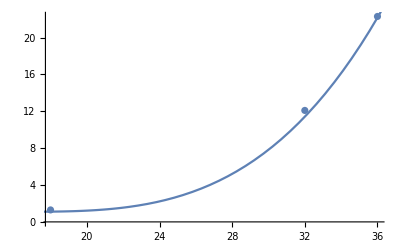

```mathematica
Show[ListPlot[{{18,1.3},{32,12.1},{36,22.3}}],Plot[1/24^3*20(x-16)^(3.2)+1.1,{x,16,40}]]
```

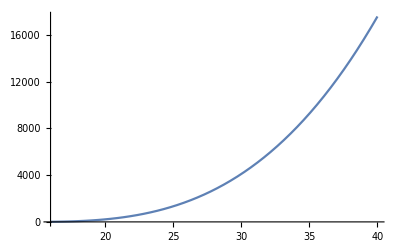

```mathematica
Plot[(x-14)^3,{x,16,40}]
```

```mathematica
`
```

```mathematica
mPred[x_]:=1/24^3*20(x-16)^(3.2)+1.1
```

```mathematica
mPred[100]
```

2081.23

```mathematica
mPredN[x_]:=1/24^3*2*(x-16)^(3.135)+1.1
```

```mathematica
mPredN[128]
```

385.422

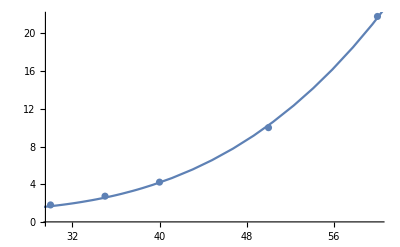

```mathematica
Show[ListPlot[{{30,1.8},{35,2.73},{40,4.22},{50,10},{60,21.8}}],Plot[1/24^3*2*(x-16)^(3.135)+1.1,{x,10,100}]]
```